# Differential Equations in Mathematica

## BYU Physics & Astronomy

## Symbolic solutions to ordinary differential equations

1D projectile
Suppose that we throw a ball straight up and wish to construct the time dependencies of the position z, velocity v, and acceleration a.  The differential equation for this situation is  
	F=m a = -m g	or	(d^2 z)/(d t^2) = -g, 
which assumes that the positive z direction is up.  

Basic usage of DSolve
We can use Mathematica’s DSolve to solve the differential equation and obtain z as a function of t.  Remembering to use “==” rather than “=” when defining equations, the syntax for defining the equation and then solving it is

```mathematica
eqns = {z''[t]==-g } 
dsols = DSolve[eqns,z[t],t]
```

Mathematica gives the solution as a double-nested list that contains a single replacement rule (the thing with the “→” in it). The inner list only contains one expression because we are only solving for one variable (i.e. z[t]).  The outer list only contains one expression because the differential equation only has one general solution.

Replacement rule solutions
Mathematica’s method of displaying solutions as a replacement rule may seem strange at first, but it is nice once you get the hang of it.  A replacement rule allows you to store your solutions for z(t) without committing your principle variable (i.e. z) to a specific solution.  We can extract the solution from the dsols list and store it in a variable with a different name (i.e. position) like this:

```mathematica
position= z[t]/.dsols[[1]]
```

Initial Conditions
We didn't specify any initial conditions above, so the solution contained unknown constants C[1] and C[2].  To include an initial condition, we give DSolve a list of equations rather than a single equation, and include the initial conditions in the list. Note that we avoid using subscripts in variable names (i.e. we use z0 instead of z_0) because subscripts can create headaches.

```mathematica
eqns = {z''[t]==-g ,z[0]==z0,z'[0]==v0} 
dsols = DSolve[eqns,z[t],t]
position= z[t]/.dsols[[1]]//Expand
```

Plotting the Solution
To plot the solution as a function of time we need to specify the values of the parameters g, z0, and v0.  Again, we use variable replacements rather than variable assignments to specify the values.  Here we use a list of replacement rules called testcase to specify the paramters, and then plot the position versus time for these parameters.

```mathematica
testcase= {g->9.8,z0->0, v0->100};
Plot[position/.testcase,{t,0,21}]
```

Evaluate the cell below, and observe that the original equations and solutions can still be viewed and utilized symbolically since we used replacements rather than assignments.

```mathematica
eqns
position
```

Working with the solution
Now that we have z(t), we can use time derivatives to obtain the velocity v(t) and acceleration a(t) and then plot them using the set of parameters stored in testcase, like this

```mathematica
velocity =D[position,t]
acceleration = D[position,{t,2}]
Plot[velocity/.testcase,{t,0,21}]
Plot[acceleration/.testcase,{t,0,21}]
```

Measuring projectile quantities
Use the plots above to visually determine how long it takes the ball to return to the ground (z = 0) and its velocity upon arrival.  We can also use Mathematica to find the time it returns to the ground by using Solve, like this

```mathematica
sol = Solve[(position/.testcase)==0,t]
returntime = t/.sol[[2]]
returnvelocity = velocity/.testcase /. sol[[2]]
```

Look at the plots again, and determine how high the ball goes before it falls back down to the ground.  We can solve this in Mathematica like this:

```mathematica
sol = Solve[(velocity/.testcase)==0,t]
peakheight = position/.testcase/.sol[[1]]
```

## Numerical solutions to ordinary differential equations

1D projectile at high speeds
Let’s consider the 1D projectile again, but instead of throwing balls we’ll launch rockets.  Since the projectile doesn’t stay near the surface of the earth  we have to use the full form of Newton’s law of gravitation: 
	(d^2 z)/(d t^2) = -G M/z^2 , 
Here G is the universal gravitational constant and M is the mass of the earth.  The addition of the z^2 term in the denomiator makes this equation nonlinear and very hard to solve analytically.  DSolve just chokes now, but its cousin NDSolve can give us a numerical solution.  

Write your equation as a set of first order equations
Second order differential equations are hard to solve directly with numerical methods.  It is better to recast them as a set of first order differential equations. For the projectile, we can just define the velocity v(t) explicitly as the first time derivative of z(t) to get a first order set, like this:  
	dz/(d t) = v	              	dv/(d t) = -G M/z^2
It is always possible to use this technique to change a higher order differential equation into a set of first order equations.  If you give NDSolve a higher order differential equation, it is smart enough to break it into a first-order set internally, but we’d like you to get in the habit of making the first order set explicitly.  When we add in the initial conditions, our set of equations becomes

```mathematica
eqns={z'[t]==v[t],v'[t]==-G*M/z[t]^2,v[0]==v0,z[0]==z0}
```

Getting a numeric solution with NDSolve
Numeric solutions can’t have variables in them because they are just a sequence of numbers representing the function values.  So, in contrast to our approach with analytic solutions, we pick values for all our parameters at the beginning with NDSolve.  We also have to specify the range of t values over which a numeric solution will be computed, since Mathematica can’t store every possible value for our solution.

In our case, the position z now represents the distance from the center of the earth, so we use z0 = 6.4×10^6 to start our projectile from the surface of the earth.  We’ll choose an initial velocity of 8,000 m/s, which is about the speed that the Saturn V rockets achieved as they left the atmosphere.  The mass of the earth and G are known constants.  For the time range, we use {t, 0, 4700}, which is about the time it takes for our rocket to come crashing back to the earth.  If you extend the time range much farther than this, Mathematica complains because the denominator goes to zero as the rocket falls to the center of the earth.

```mathematica
testcase={M->6 10^24 ,G->6.67×10^-11, v0->8 10^3,z0->6.4 10^6}
tmin = 0; tmax =4700;
nsols = NDSolve[eqns/.testcase,{z[t],v[t]},{t,tmin,tmax}]
```

The solutions appear as nested lists of replacement rules like they did with DSolve.  However, each replacement object is now a numerical object called an InterpolatingFunction over the variable t. An interpolating functions is essentially a table of numbers that Mathematica uses to represent a function at various values of t.  If you ask the interpolating function for a value of the t that is not in the table, Mathematica interpolates or extrapolates between or beyond the values in the table to give you a good estimate of the value.

We can store the interpolating functions in a variables and plot them, like this

```mathematica
position= z[t]/.nsols[[1]]
velocity =v[t]/.nsols[[1]]
Plot[position,{t,0,4500}]
Plot[ velocity,{t,0,4500}]
```

Working with InterpolatingFunctions
Interpolating functions can be treated much like any other function of t.  Here is how you take the derivative of velocity to find acceleration:

```mathematica
velocity =D[position,t]
acceleration = D[position,{t,2}]
Plot[ acceleration,{t,0,4500}]
```

Notice that the acceleration is not constant now since our projectile moves a significant distance from the surface of the earth.

We can use our interpolating functions to calculate how long it takes the rocket to fall back to the earth. Interpolating functions are inherently numeric, so we rephrase this problem as a numeric root-search operation.  Given a reasonably good initial guess, Mathematica's FindRoot function will numerically find a nearby root (a place where the function is zero).  We will use t = 4,000 as the initial guess, which we obtained visually from the z(t) graph above.

```mathematica
sol =FindRoot[position-6.4 10^6,{t,4000}]
returntime = t/.sol
returnvelocity = velocity/.sol
```

For scale, it may be helpful to recall that there are 3,600 s in an hour.  Note that the return velocity is not exactly the initial velocity because numerical solutions have an inherent amount of error.

Using a similar technique, we can etermine how high the rocket went before it fell back down to the ground.  We again use FindRoot, starting with an approximate peak position obtained from the z(t) graph above.

```mathematica
sol = FindRoot[velocity,{t,2000}]
peakheight = position/.sol
```

For scale, it may be helpful to recall thatthe moon orbits at about 3.8×10^8 m.  You’ll notice that we didn’t quite achieve a moon-shot with our Saturn V.  When we really went to the moon, this first phase just got the rocket into earth orbit.  Once they were sure everything was OK in earth orbit, they did another long burn to send the rocket on an energy-efficient curved path to the moon.  We’d need to use a 2D model to simulate the actual flight path.

## Phase Space

When we break a second order differential equation into a set of first-order equations, it naturally creates a set of coordinates that lend themselves to a type of 2D graphical representation called phase space.  We can use these coordinates to visualize the behavior of the system with many different initial conditions without having to actually solve the equations.

Let’s see how this works by considering the 1D projectile with the constant acceleration again.  The system of differential equation for this case is
	dz/(d t) = v		and		dv/(d t) = -g
Position z and velocity v are the axes that define phase space for this system. At any point in time t the coordinate  {z(t), v(t)} gives the phase-space point that represents the “state” of the system.  Given an initial starting point, {z0, v0}, this point will move in time to trace out a curve called a phase space trajectory.  

Flow plots
If we solve the differential equation, we can plot these trajectories, but we can get a feel for the solution by thinking of dv/dt and dz/dt as flow velocities in a fluid problem. This type of visualization is called a flow plot.  To get a feel for what a flow plot is, think of air flow on a two-dimensional map.  Here the coordinates are x and y and the flow velocities dx/dt and dy/dt give the wind velocity at a given point.

Mathematica can plot the flow velocities for a differential equation like this

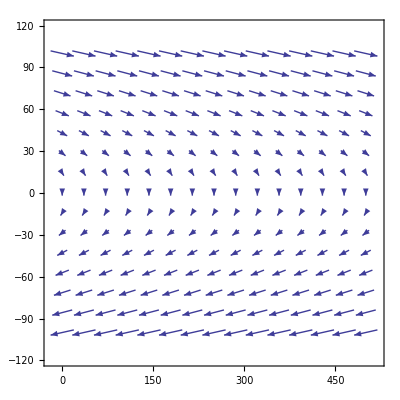

```mathematica
VectorPlot[{v,-9.8},{z,0,500},{v,-100,100}]
```

Compare the inputs to VectorPlot with the differential equations in our first order system and explain to your lab partner where the plotted quantities come from. Especially note that you didn’t have to solve the differential equation to write down the flow velocities.

Often it is helpful to add some “stream lines” which show the phase-space trajectory that a system will follow from a given state.  Adding some plot options to VectorPlot, we can visualize the trajectories like this

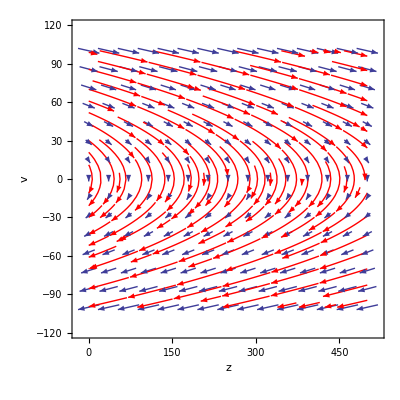

```mathematica
poptions = {StreamPoints->Fine, StreamStyle->{Thick,Red},StreamScale->Large,FrameLabel->{z,v}};
flow =VectorPlot[{v,-9.8},{z,0,500},{v,-100,100},Evaluate[poptions]]
```

Note that the options have to be Evaluated when brought inside the VectorPlot.  Discuss this plot with your lab partner until you can both explain what it represents.

Manually adding trajectories to a flow plot
Sometimes Mathematica gets confused and can’t put the stream lines (ti.e. rajectories) on a flow plot automatically.  This is the case for the high-speed 1D projectiles, where gravity is described by Newton’s law of gravitation:
	dv/(d t) = -G M/z^2	 and  	dz/(d t) = v
When we ask Mathematica to put the stream lines on the plot, it can make the vector arrows, but it can’t figure out the stream lines

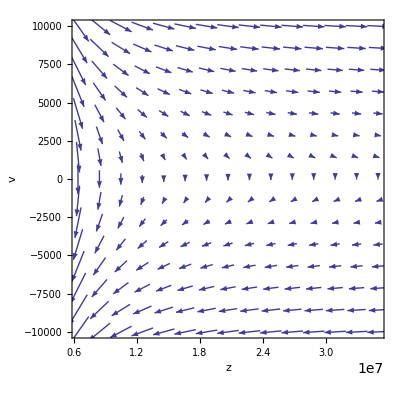

```mathematica
a =-G*M/z^2/.{M->6 10^24 ,G->6.67×10^-11 };
poptions =  {PlotRange->{{6.4 10^6,3.5 10^7},{-10000,10000}},AspectRatio->1,FrameLabel->{z,v}};
flow =VectorPlot[{v,a},{z,6.4 10^6,3.5 10^7},{v,-10000,10000},Evaluate[poptions]]
```

We can still sort of visualize what the trajectories would look like, but it would be nice t see them visually.

To put trajectories on the plot manually, we have to solve the differential equation.  In this case, we need to solve it numerically.  We can solve the differential equation for several initial conditions like this

```mathematica
eqs={z'[t]==v[t],v'[t]==-G*M/z[t]^2,v[0]==v0,z[0]==z0}
params={M->6 10^24 ,G-> 6.67 10^-11,z0->6.4 10^6}
numeqs = eqs/.params;

case1={z[t],v[t]}/.Flatten[NDSolve[numeqs/.v0->5000,{z[t],v[t]},{t,0,1500}]]
case2={z[t],v[t]}/.Flatten[NDSolve[numeqs/.v0->7500,{z[t],v[t]},{t,0,3900}]]
case3={z[t],v[t]}/.Flatten[NDSolve[numeqs/.v0->10000,{z[t],v[t]},{t,0,19500}]]
```

{z'[t]==v[t],v'[t]==-(G M)/z[t]^2,v[0]==v0,z[0]==z0}

{M→6000000000000000000000000,G→6.67×10^-11,z0→6.4×10^6}

{InterpolatingFunction[{{0.,1500.}},<>][t],InterpolatingFunction[{{0.,1500.}},<>][t]}

{InterpolatingFunction[{{0.,3900.}},<>][t],InterpolatingFunction[{{0.,3900.}},<>][t]}

{InterpolatingFunction[{{0.,19500.}},<>][t],InterpolatingFunction[{{0.,19500.}},<>][t]}

Now we can make plots of a bunch of phase space trajectories and overlay them using ParametricPlot

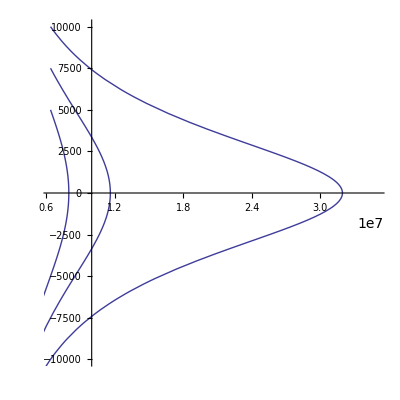

```mathematica
trajectory1 = ParametricPlot[case1,{t,0,1500},Evaluate[poptions]];
trajectory2 = ParametricPlot[case2,{t,0,3900},Evaluate[poptions]];
trajectory3 = ParametricPlot[case3,{t,0,19500},Evaluate[poptions]];
trajectories = {trajectory1,trajectory2,trajectory3};
Show[trajectories]
```

Then we can overlay the trajectories on the flow plot, like this

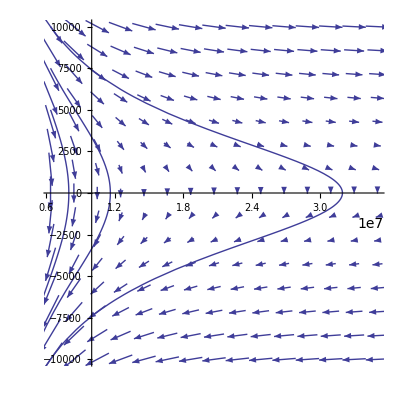

```mathematica
Show[trajectories,flow]
```

## Partial differential equations

### PDE general solutions

The following example is straightforward, but not explained in any detail here.  See the PDE subsections within the Scope sections of the DC reference pages for DSolve and NDSolve for more examples.

```mathematica
eqns = {3D[y[x1,x2],x1]+5D[y[x1,x2],x2]==x1}
dsols = DSolve[ eqns,y[x1,x2],{x1,x2}]
result = y[x1,x2]/.dsols[[1]]/. C[1]->Sin
Plot3D[result,{x1,-5,5},{x2,-5,5},AxesLabel->{"X1","X2","Y"}]
```

### PDEs with boundary conditions

```mathematica
eqns = {3D[y[x1,x2],x1]+5D[y[x1,x2],x2]==x1,y[x1,0]==0}
dsols = DSolve[ eqns,y[x1,x2],{x1,x2}]
result = y[x1,x2]/.dsols[[1]]
Plot3D[result,{x1,-5,5},{x2,-5,5},AxesLabel->{"X1","X2","Y"}]
```

### Numerical solutions to PDEs

```mathematica
eqns = {3D[y[x1,x2],x1]+5D[y[x1,x2],x2]==x1,y[x1,0]==0}
min1 = -5; max1 = 5; min2 = -5; max2 = 5;
dsols = NDSolve[ eqns,y[x1,x2],{x1,min1,max1},{x2,min2,max2}];
result = y[x1,x2]/.dsols[[1]]
Plot3D[result,{x1,min1,max1},{x2,min2,max2},AxesLabel->{"X1","X2","Y"}]
```

## Further Reading

### 1D Projectile with Drag

(a) Let's revisit the 1D projectile with the addition of linear viscous drag.  The differential equation now has the form  (d^2 z)/(d t^2) = - g-b/m dz/dt, where the drag coefficient (b) has units of kg/sec.

```mathematica
eqns = {z''[t]==-g -(b/m)*z'[t],z[0]==z0,z'[0]==v0} 
dsols = DSolve[eqns,z[t],t];

position= z[t]/.dsols[[1]]//Expand 
velocity =D[position,t]
acceleration = D[position,{t,2}]
```

(b) Evaluate the cell below, and observe that in the limit that b → 0 (no air resistance), these expressions revert to the form that you are already familiar with.  Note that a simple variable replacement won't work here, since eliminating b fundamentally changes the original differential equation.

```mathematica
Limit[{position,velocity,acceleration},b->0]
```

(c) Evaluate and graph the time dependencies of position, velocity and acceleration for a specific case.  How and why do these results differ from those of the zero-resistance case?

```mathematica
testcase= {m -> 1, g -> 10, b -> 0.3, z0 -> 0, v0 -> 100};
{position, velocity, acceleration}/.testcase
Plot[#,{t,0,20}]& /@ %
```

(d) Determine how long it takes the ball to return to the ground (z = 0) and its velocity upon arrival.  The additional messages generated here warn you that Mathematica is inverting transcendental functions and may not find all possible solutions.  However, because this is a fairly simple example, Mathematica does find all possible solutions, including the one that we are interested in.

```mathematica
sol =Solve[(position/.testcase)==0,t]
returntime = t/.sol[[2]]
returnvelocity = velocity/.testcase /. sol[[2]]
```

(e) Determine how high the ball will go before it falls back down to the ground, and observe that we can use Quiet to preempt the unwanted warning messages about inverse functions.

```mathematica
sol = Solve[(velocity/.testcase)==0,t]//Quiet
peakheight = position/.testcase/.sol[[1]]
```

### Coupled mass-spring oscillators

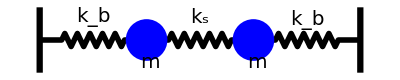

```mathematica
motif= Line[Join[{{-8.5,0},{-5,0}},Table[{-4.5+n,(-1)^n},{n,0,9}],{{5,0},{8.5,0}}]];

spring1 = motif//Translate[#,{-17,0}]&;
spring2 = motif;
spring3 = motif//Translate[#,{17,0}]&;

joints = {Rectangle[{-26,-5},{-25,5}],{Blue,Point[{-8.5,0}],Point[{8.5,0}]},Rectangle[{25,-5},{26,5}]};
annote[{txt_,dirs_,pt_}]:= Text[Style[txt,dirs,FontSize->20],pt]
annotations = annote/@{{"k_b",{},{-17,3.5}},{"m",{},{-8,-3.5}},{"k_s",{},{0,3.5}},{"m",{},{9,-3.5}},{"k_b",{},{17,3}}};
network = {Thickness[0.01],PointSize[0.075],spring1,spring2,spring3,joints,annotations};
Graphics[network]
```

In the mass-spring network above, assume that none of the springs are stretched when the system is in equillibrium.  Consider the time-dependences of the positions of the two masses, x_1(t) and x_2(t), which we define so as to be zero at their equillibrium positions. If the central spring is absent, F = m a = 0 yields m d^2/(d t^2)x_1 = -k_b x_1 for the first spring and m d^2/(d t^2)x_2 = -k_b x_2 for the second.  When the central spring is added, these equations become m d^2/(d t^2)x_1 + k_b x_1 - k_s (x_2-x_1) = 0 and m d^2/dt^2 x_2 + k_b x_2 - k_s (x_1-x_2) = 0, which can also be combined into matrix form as  d^2/(d t^2)x + M·x = 0, where M is a matrix that depends on the spring constants and masses of the network, and x =(x_1
x_2) is a vector containing the two time-dependent positions.

(a) We construct the matrix M associated with these equations.

```mathematica
M = {{kb+ks,-ks},{-ks,kb+ks}}/m;
MatrixForm[M]
```

(b) Next, we use M to construct the equations of motion.  The Thread function is helpful here for converting an equation between two pairs into a pair of equations.

```mathematica
unknowns ={x1[t],x2[t]};
derivs = D[unknowns,{t,2}]
derivs+M.unknowns=={0,0}
diffeq = Thread[%]
```

(c) Evaluate the cell below to solve for the time-dependent positions of the two masses.  The result should look pretty hairy.

```mathematica
eqns = {diffeq,x1[0]==x10,x1'[0]==v10,x2[0]==x20,x2'[0]==v20};
positions = unknowns/.DSolve[{eqns,inits},unknowns,t][[1]]
```

(d)  We evaluate the time-dependent positions of the two masses for the special case where the central spring is much weaker than the springs on either side (i.e. k_b → 1 and k_s → 0.1), and m → 1, and all of the initial velocities and positions are zero except for x_10 → 1.  Observe that due to weak coupling, the vibrational energy is passed back and forth between the two masses (red and blue).  While the time dependence is purely real, we have explicity singled out the real part in order to eliminate imaginary round-off errors that would otherwise interfere with the graph.

```mathematica
testcase = {kb->1,ks->0.1,m->1,x10->1, x20->0,v10->0,v20->0};
positions /.testcase//Re//ComplexExpand
Plot[%,{t,0,30Pi},PlotStyle->{{Thick,Red},{Thick,Blue}}]
```

### Harmonic oscillator

The harmonic oscillator appears in a remarkable variety of physical systems (electrical, mechanical, accoustical and quantum mechanical).  It’s differential equation is given by (d^2 z)/(d t^2) = - ω_0^2z, where ω_0 is the natural frequency of the oscillator, we obtain its sinusoidal time-dependence in terms of the initial conditions on position and velocity.  As before, we solve this together with initial conditions like this

```mathematica
eqns = {x''[t] == -ω0^2 x[t], x[0]==x0, x'[0]==v0};
position= x[t]/.DSolve[eqns,x[t],t][[1]]//Simplify
velocity = D[position,t]
```

For the special case in which the natural frequency of the oscillator is ω0 = 2π, and in which the initial conditions are x0 = 1 and v0 = 0, we plot both the position (Red) and the velocity (Blue) on the same graph.  The position and the velocity are 90° out of phase so that the oscillator has zero velocity at the point of maximum position and vice versa.  We chose to apply the natural frequency and the initial conditions separately here to set an example that will prove convenient in later exercises.

```mathematica
testcase = {ω0->2Pi}; init = {x0->1,v0->0};
{position,velocity}/.testcase/.init
Plot[%,{t,0,10},PlotStyle->{Red,Blue}]
```

### Harmonic oscillator

(a) The harmonic oscillator in the previous exercise consisted of a single second-order differential equation in one variable, x(t).  We will now recast this problem as a system of two first-order differential equations in two variables, x(t) and v(t), noting that the velocity, v(t) is the first time derivative of x(t).  Because we now have more than one unknown variables, it will be convenient to group them together in a list called unknowns.  DSolve then returns the same result obtained above.

```mathematica
eqns = {x'[t]==v[t],v'[t] == -ω0^2 x[t], x[0]==x0, v[0]==v0};
unknowns = {x[t],v[t]};
{position,velocity}=unknowns/.DSolve[eqns,unknowns,t][[1]]//Simplify
```

(b) For the special case in which the natural frequency of the oscillator is ω0 = 2π, and in which the initial conditions are x0 = 1 and v0 = 0, we also obtain the same graphs obtained above.

```mathematica
testcase = {ω0->2Pi}; init = {x0->1,v0->0};
{position,velocity}/.testcase/.init
Plot[%,{t,0,10},PlotStyle->{Red,Blue}]
```

(c) However, the new two-variable (i.e. x(t) and v(t)) way of thinking about the problem lends itself to a new type of 2D graphical representation called phase space.  Let x and v be axes that define this space and let {x(t), v(t)} be the phase-space point that represents the "state" of the system at time t.  Given an initial starting point, {x0, v0}, this point will move in time to trace out a curve called a trajectory.  In the example below, we define a list of initial conditions, and compute each resulting trajectory in parametric form.  Because inits is a list of four replacement rules rather than a single rule, its application produces a list of four trajectories rather than a single trajectory.

```mathematica
testcase = {ω0->2Pi}; inits = Table[{x0->n,v0->0},{n,0.5,2,0.5}]
trajectorylist = {position,velocity}/.testcase/.inits
```

(d)  The function for graphing parametric functions in 2D is ParametricPlot.  Because we'll need a fair number of options to make the resulting graph look nice, it will be convenient to define all of the plot options on a separate line.  But this convenience comes with a price -- the options have to be Evaluated when brought inside the plot function.  This truly obnoxious offense arises because most common plot functions have the default HoldAll attribute, which prevents their arguments from being evaluated automatically.  Until the powers that be hear our complaints, you'll just have to get used to this.  Note that we strategically chose the PlotRange and the AspectRatio to make the trajectories appear circular.  We also computed the trajectories over the range from 0 to 1 so as to obtain a full circle.  Try lowering the upper limit of the time range.

```mathematica
poptions = {AspectRatio->1,AxesLabel->{"x","v"},PlotRange->{{-2,2},{-4Pi,4Pi}}, PlotStyle->Thick};
trajectoryplot = ParametricPlot[trajectorylist,{t,0,1},Evaluate[poptions]]
```

(d)  The time derivative of the phase-space point, ℱ = {x'(t), v'(t)}, is also a parametric vector field that we will call the flow.  This flow field  is readily obtained from the original system of equations.  For the harmonic oscillator, we can see by inspection that ℱ = {v, -ω0^2x}.  But for good measure, we also demonstrate the proper approach for extracting the flow in non-parametric form from the equations of motion.

```mathematica
derivs = {x'[t],v'[t]};
flow = derivs/.Solve[eqns,derivs][[1]]/.testcase
```

(e)  Mathematica has some very nice functions for graphing vector fields.  In the 2D plane, these include VectorPlot and StreamPlot.  Using plot options similar to those above, we demonstrate the application of VectorPlot, which really ought to be simple.  In practice, it is quite painful to get the lengths and sizes of the arrowheads to behave reasonably (see the VectorScale option)!

```mathematica
poptions = {AspectRatio->1,AxesLabel->{"x","v"},PlotRange->{{-2,2},{-4Pi,4Pi}},VectorScale->{0.1,0.2}};
flowplot = VectorPlot[flow,{x[t],-2,2},{v[t],-4Pi,4Pi},Evaluate[poptions]]
```

(e)  Now, we superimpose the trajectory plot and the flow plot onto a single graph.  Pretty impressive until you compare it to Maple's DEplot function, which makes the generation of flow/trajectory plots like this a one-line breeze.

```mathematica
Show[flowplot,trajectoryplot]
```

### Damped driven harmonic oscillator

Revisiting the harmonic oscillator again, we'll raise the complexity a bit by adding linear damping (friction) and a sinusoidal driving force: m(d^2 z)/(d t^2) + m ω_0^2 z+b(d z)/(d t)=A cos(ω t).  Here, ω_0 is the undamped natural frequency, ω the driving frequency, m the mass, b the damping coefficient, and A the driving-force amplitude.  As in the previous exercise, we first evaluate the system of equations numerically for a specific case, and use NDSolve to solve the equations numerically over a predefined range of t.  The resulting time dependence illustrates the exponential decay of transient beating, after which only a weak steady-state oscillation persists at the driving frequency.

```mathematica
testcase = {A->1,b->0.05,m->1,ω0->1,ω->0.8}; inits = {x0->20,v0->0}
eqns = {m x''[t] == -m ω0^2 x[t]-b x'[t]+A Cos[ω t], x[0]==x0, x'[0]==v0}/.testcase/.inits
tmin = 0; tmax =80*Pi;
nsols = NDSolve[eqns,x[t],{t,tmin,tmax}]
position = x[t]/.nsols[[1]]
Plot[position,{t,tmin,tmax},PlotRange->All,PlotPoints->50]
```

### Nonlinear dynamics and chaos

Here is a more advanced example involving a nonlinear system of first-order differential equations in three spatial variables, x(t), y(t) and z(t).  These equations were originally applied to weather prediction by Ed Lorenz, which led him to discover what we now call chaos theory.  Instead of converging to a stable limit cycle, the resulting trajectory jumps back and forth chaotically between two regions of phase space that comprise a "strange attractor".  ParametricPlot3D provides a nice way to visualize 3D trajectories like this.

```mathematica
eqns = {x'[t]==-σ*(x[t]-y[t]),y'[t]==r*x[t]-y[t]-x[t] z[t],z'[t]==x[t] y[t]-b*z[t],x[0]==z[0]==0,y[0]==1} /. {σ->10,b->8/3,r->50}
unknowns = {x[t],y[t],z[t]}; 
tmin = 0; tmax =10;
nsols=NDSolve[eqns,unknowns,{t,tmin,tmax},MaxSteps->Infinity]
trajectory = unknowns/.nsols[[1]];
ParametricPlot3D[trajectory,{t,tmin,tmax},PlotPoints->50]
```